# On a four-dimensional oncolytic Virotherapy model (ϵ=1)

This Mathematica Notebook is a supplementary material to the paper “On a three-dimensional and two four-dimensional
oncolytic viro-therapy models”. It contains some of the calculations and illustrations appearing in the paper.

## Ep1)Section 3.5(in paper): 4-Dim.Viro-therapy model when ϵ=1

### Ep1-1)Definition of the model and fixed points when ϵ=1

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
Clear["K"];
(*Some aliases*)
Format[βy]=Subscript[β,y];Format[βv]=Subscript[β,v];Format[βz]=Subscript[β,z];


Unprotect[Power];
Power[0,0]=1;
Protect[Power];

par={b,β,λ,δ,βy, βv,βz,c,γ,K,ϵ};
cp=Join[Thread[Drop[par,{1}]>0],{b>1}];
cKga1={K->1,γ->1};
cep1={ϵ->1};
R0=b β K/(β K+δ)(* Reproduction number*);

(*cnb={b->50};
cE1ri=Join[{βy->1/48,K->2139.258, β->.0002,λ->.2062,γ->1/18,δ->.025, βv->2*10^(-8),c->10^(-3),βz->.027},cep1];*)
cF1={β->87/2,λ->1,γ->1/128,δ->1/2,βy->1,βv->1,K->1,βz->1,c->1,ϵ->1};

(****** Four dim Deterministic  epidemic model with Logistic growth ****)
x1=λ  x(1-(x+y)/K)-   β x v ;
y1=β x v -βy y z- γ y;
v1=-β x v - βv  v z+ b  γ y - δ v;
z1=z(βz  y - c z^ϵ);
dyn={x1,y1,v1,z1};
dyn3={x1,y1,v1}/.z->0;(*3dim case used for E* *)
Print[" (x'
y'
v'
z')=",dyn//FullSimplify//MatrixForm]
Print["b0=",b0=b/.Apart[Solve[R0==1,b][[1]]//FullSimplify]]

(***Fixed point when z->0**)
eq=Thread[dyn3=={0,0,0}];
sol=Solve[eq,{x,y,v}]//FullSimplify;
Es={x,y,v}/.sol[[3]];(*Endemic point with z=0*);
Print[" Endemic point with z=0 is E*=",Es//FullSimplify]
jacD=Grad[dyn/.cep1,{x,y,v,z}];
Print["J(x,y,v,z)="]
jacD//MatrixForm
Print["Det(J(x,y,v,z))="]
Det[jacD]//FullSimplify
```

(x'
y'
v'
z')=(-v x β+x (1-(x+y)/K) λ
v x β-y (z β_y+γ)
b y γ-v (x β+z β_v+δ)
z (-c z^ϵ+y β_z))

b0=1+δ/(K β)

Endemic point with z=0 is E*={δ/((-1+b) β),(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)),(γ ((-1+b) K β-δ) λ)/(β ((-1+b) K β γ+δ λ))}

J(x,y,v,z)=

(-v β-(x λ)/K+(1-(x+y)/K) λ | -(x λ)/K | -x β | 0
v β | -z β_y-γ | x β | -y β_y
-v β | b γ | -x β-z β_v-δ | -v β_v
0 | z β_z | 0 | -2 c z+y β_z)

Det(J(x,y,v,z))=

1/K(2 c z (K v β (z β_y+γ) (z β_v+δ)+v x β (z β_v+δ) λ-K (x β (z β_y+γ-b γ)+(z β_y+γ) (z β_v+δ)) λ+(2 x+y) (x β (z β_y+γ-b γ)+(z β_y+γ) (z β_v+δ)) λ)-β_z (K y γ ((-1+b) x β-z β_v-δ) λ-y (2 x+y) γ ((-1+b) x β-z β_v-δ) λ+v x β (-2 x z β_v+y δ) λ+K v β (y γ (z β_v+δ)+x z β_v λ)))

f(y)=-y β_y β_z+(-1+b) c γ ,g(y)=y β_v β_z+c δ , h(y)=(y β_y β_z)/c+γ

p(y)=(y β (y β_y β_z-(-1+b) c γ))/(y β_v β_z+c δ)+λ-(y λ)/K-(((y β_y β_z)/c+γ) (y β_v β_z+c δ) λ)/(K β (-y β_y β_z+(-1+b) c γ))

The polynomial  Q(y) is of order  3

Coefficients of Q(y) are {(c^2 γ ((-1+b) K β-δ) δ λ)/(K β),-(c (β_z (δ (2 β_v γ+β_y δ)+K β (β_v γ-b β_v γ+β_y δ)) λ+(-1+b) c β γ ((-1+b) K β γ+δ λ)))/(K β),(β_z (-β_v β_z (K β β_y+β_v γ+2 β_y δ) λ+c β (2 (-1+b) K β β_y γ+β_v (γ-b γ) λ+β_y δ λ)))/(K β),-(β_y β_z^2 (β_v^2 β_z λ+c β (K β β_y-β_v λ)))/(c K β)}

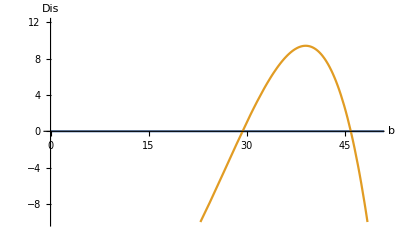

Roots of Dis[b]=0 are: {{b→-126.518},{b→-63.},{b→-63.},{b→-24.5518},{b→29.361},{b→45.9232}}

```mathematica
(*****Fixed points of 4-dim model using P(y)***)
fy=(c γ(b-1)-y βy βz);
gy=( βv βz y+c δ); hy=(γ +y βz βy/c);
xey=hy gy/(β fy); vey=y fy/gy; zey= βz y /c;
ys=y/.sol[[3]](* y of E*     ****);

Py=λ(1-y/K)-β y fy/gy-λ hy gy/(β K fy); yb=c γ (b-1)/(βy βz);
Qy=λ fy gy(1-  y /K)- λ hy gy^2/(β K)-y β fy^2;
Qycol=Collect[Together[Qy],y];
Qycoef=CoefficientList[Qycol,y];
Print["f(y)=", fy, " ,g(y)=", gy, " , h(y)=", hy]
Print["p(y)=", Py//FullSimplify]
Print["The polynomial  Q(y) is of order  ", Length[Qycoef]-1]
Print["Coefficients of Q(y) are ", Qycoef//FullSimplify]

Dis=Collect[Discriminant[Qy,y],b];
Discoef=CoefficientList[Dis,b];Length[Discoef];
Disn=Dis//.cF1//N;
bL=50;
Plot[{0,Disn},{b,0,2 bL},AxesLabel->{"b","Dis"},PlotRange->{{0,bL},{-10,12}}]
Print["Roots of Dis[b]=0 are: ",solbE=Solve[Disn==0,b]]
```

```mathematica
QR=Solve[Qy==0,y,Cubics->False]//ToRadicals(*casus irreducibilis*);
ym= y/.QR[[2]];
yp=  y/.QR[[1]];yi=  y/.QR[[3]];
Em1={xey,ym,vey,zey}//.y->ym;
Ep1={xey,yp,vey,zey}//.y->yp;
Eim1={xey,yi,vey,zey}//.y->yi;
Es1=Join[{x,y,v}/.sol[[3]],{0}];
{Chop[yp],Chop[ym]}//.cF1//N;

jacE1K=jacD/.x->K/.y->0/.v->0/.z->0;
Print["J(EK)=", jacE1K//MatrixForm]
(*Jacobians of the fixed points**)
jEs1=jacD/.sol[[3]]/.z->0;
jEm1=jacD/.x->xey/.v->vey/.z->zey/.y->ym;
jEim1=jacD/.x->xey/.v->vey/.z->zey/.y->yi;
jEp1=jacD/.x->xey/.v->vey/.z->zey/.y->yp;
Print["Eig.val of J(EK) are:", Eigenvalues[jacE1K]//FullSimplify]
jacE1=jacD/.x->xey/.v->vey/.z->zey/.y->y//FullSimplify;
jacE1 //MatrixForm;
Det[jacE1]//FullSimplify;
Print[" Trace of either Ei, E+ or E- is : ", Tr[jacE1]//FullSimplify]
Print["J(E_*) is"]
jEs1//FullSimplify//MatrixForm
bbs=b/.Solve[yb==(y/.sol[[3]]),b][[1]](*long expression*);
```

J(EK)=(-λ | -λ | -K β | 0
0 | -γ | K β | 0
0 | b γ | -K β-δ | 0
0 | 0 | 0 | 0)

Eig.val of J(EK) are:{0,1/2 (-K β-γ-δ-√(-4 γ (K (β-b β)+δ)+(K β+γ+δ)^2)),1/2 (-K β-γ-δ+√(-4 γ (K (β-b β)+δ)+(K β+γ+δ)^2)),-λ}

Trace of either Ei, E+ or E- is : -y β_z-(y β_y β_z+c γ)/c+(y^2 β β_y β_z)/(y β_v β_z+c δ)-((-1+b) c y β γ)/(y β_v β_z+c δ)+(b γ (y β_v β_z+c δ))/(y β_y β_z-(-1+b) c γ)+λ-(y λ)/K-(2 ((y β_y β_z)/c+γ) (y β_v β_z+c δ) λ)/(K β (-y β_y β_z+(-1+b) c γ))

J(E_*) is

((δ λ)/(K β-b K β) | (δ λ)/(K β-b K β) | -δ/(-1+b) | 0
(γ ((-1+b) K β-δ) λ)/((-1+b) K β γ+δ λ) | -γ | δ/(-1+b) | (β_y δ (K (β-b β)+δ) λ)/((-1+b) β ((-1+b) K β γ+δ λ))
(γ (K (β-b β)+δ) λ)/((-1+b) K β γ+δ λ) | b γ | (b δ)/(1-b) | (β_v γ (K (β-b β)+δ) λ)/(β ((-1+b) K β γ+δ λ))
0 | 0 | 0 | (β_z ((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)))

Hopf bifurcation point related  to b- for E- :

```mathematica
(*it takes few minutes to run*)
cn=Join[cF1]; 
pcm=Collect[Det[ψ IdentityMatrix[4]-(jEm1)],ψ];
coT=CoefficientList[pcm,ψ];
Length[coT]
a1=coT[[4]] ;a2=coT[[3]];a3=coT[[2]] ; a4=coT[[1]];
H4m=a1*a2*a3-a3^2+a1^2 a4//.cF1;
ϕb4m=Collect[Numerator[Together[H4m]],b];
cbm=NSolve[(ϕb4m//.cn)==0,b,WorkingPrecision->10];
bMm=Max[Table[Re[b/.cbm[[i]]],{i,Length[cbm]}]];
Print["bH-=",bHm=N[bMm,30]]
```

5

bH-=29.19440675

### Ep1-2)Trace, Det and third criterion of Routh Hurwitz applied to E*:

Det and Trace of of E* and Analysis of the stability of E* in 4 dim when ϵ=1:

```mathematica
Print["Tr[J[E*]]="]
trEs1=Tr[jacD//.Join[sol[[3]],{z->0}]]//FullSimplify
Print["Det[J[E*]]="]
detEs1=Det[jacD//.Join[sol[[3]],{z->0}]]//FullSimplify

pc=Collect[Det[ψ IdentityMatrix[4]-(jEs1)],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Length[coT]
a1=coT[[4]]//FullSimplify ;a2=coT[[3]]//FullSimplify;a3=coT[[2]]//FullSimplify ; a4=coT[[1]]//FullSimplify;
Print["a_1=",a1, ", a_2=",a2, ", a_3=",a3, " ,a_4=", a4 ]
H4=a1*a2*a3-a3^2+a1^2 a4;
Print["H2(b0)=",H4/.b->b0//FullSimplify]
Print["Denominator of H2 is ",Denominator[Together[H4]]//FullSimplify]
ϕb4=Collect[Numerator[Together[H4]],b];
cofi=CoefficientList[ϕb4,b];
Length[cofi]
(*Print["value of ϕ(b) at crit b is "]
ϕb4/.b->b0//FullSimplify; (*so long expression*)*)
```

Tr[J[E*]]=

-(K δ (2 (-1+b) β γ+b β δ+β_z δ) λ+δ^2 λ^2+(-1+b) K^2 β (β γ ((-1+b) γ+b δ)-β_z δ λ))/((-1+b) K β ((-1+b) K β γ+δ λ))

Det[J[E*]]=

-(β_z γ δ^2 (K (β-b β)+δ)^2 λ^2)/((-1+b)^2 K β^2 ((-1+b) K β γ+δ λ))

5

a_1=(K δ (2 (-1+b) β γ+b β δ+β_z δ) λ+δ^2 λ^2+(-1+b) K^2 β (β γ ((-1+b) γ+b δ)-β_z δ λ))/((-1+b) K β ((-1+b) K β γ+δ λ)), a_2=((δ λ (-((-1+b) K^2 β^2 ((-1+b) (β+β_z) γ+b β_z δ))+(b β+β_z) δ^2 λ+K β (β_z δ ((-1+b) γ+b δ+λ-b λ)+(-1+b) β γ ((-1+b) γ+δ-λ+b (δ+λ)))))/((-1+b)^2 K β^2 ((-1+b) K β γ+δ λ))), a_3=((((-1+b) K β-δ) δ λ (δ^2 ((-1+b)^2 β γ-b β_z δ) λ^2+(-1+b)^2 K^2 β^2 γ ((-1+b)^2 β γ^2+β_z δ λ)+(-1+b) K β γ δ λ (2 (-1+b)^2 β γ-β_z ((-1+b) γ+δ-λ+b (δ+λ)))))/((-1+b)^3 K β^2 ((-1+b) K β γ+δ λ)^2)) ,a_4=-(β_z γ δ^2 (K (β-b β)+δ)^2 λ^2)/((-1+b)^2 K β^2 ((-1+b) K β γ+δ λ))

H2(b0)=0

Denominator of H2 is (-1+b)^6 K^3 β^5 ((-1+b) K β γ+δ λ)^4

11

Numerical values ϵ=1:

```mathematica
cn=Join[cF1]; cnb={b->40};
cb=NSolve[(ϕb4//.cn)==0,b,WorkingPrecision->10]
bM=Max[Table[Re[b/.cb[[i]]],{i,Length[cb]}]];
Print["bH=",bH=N[bM,30]]
Print["b0=",b0/.cn//N]

Print["E*",Es1//.cn/.cnb//N]
Print["E+=",Em1//.cn/.cnb//N]
Print["Eim=",Eim1//.cn/.cnb//N]
Print["roots of Dis[b]=0:", bcE1=NSolve[(Dis//.cn)==0,b]]
bc1=Chop[Evaluate[b/.bcE1[[5]]]];
bc2=Chop[Evaluate[b/.bcE1[[6]]]];
Print["b1*=", bc1]
Print[" b2*=", bc2]
```

{{b→-258.7317419},{b→-0.01615999598},{b→0.06084806-10.68699074 ⅈ},{b→0.06084806+10.68699074 ⅈ},{b→0.844828267-0.9299250641 ⅈ},{b→0.844828267+0.9299250641 ⅈ},{b→0.8878046288},{b→1.011494253},{b→1.022996712},{b→1.152364263}}

bH=1.152364263

b0=1.01149

E*{0.000294724,0.0363426,0.0221463,0.}

E+={0.00262408+5.51068×10^-19 ⅈ,0.0462057+8.67362×10^-18 ⅈ,0.021866+3.02367×10^-18 ⅈ,0.0462057+8.67362×10^-18 ⅈ}

Eim={0.114678-9.26732×10^-17 ⅈ,0.263221-2.77556×10^-17 ⅈ,0.0143012+8.58446×10^-18 ⅈ,0.263221-2.77556×10^-17 ⅈ}

roots of Dis[b]=0:{{b→-126.518},{b→-63.},{b→-63.},{b→-24.5518},{b→29.361},{b→45.9232}}

b1*=29.361

b2*=45.9232

### Ep1-3)Bifurcation diagrams :

Numerical solution of the stability (Bifurcation diagram) wrt y:

```mathematica
(*Checks on the stability of the fixed points**)
Print["Eigenvalues of E* when b=20 and when b=40, respectively "]
Eigenvalues[jEs1]//.cF1/.b->20//N
Eigenvalues[jEs1]//.cF1/.b->40//N
Print["Eigenvalues of E+  when b=40"]
Chop[Eigenvalues[jEp1//.cF1/.b->20//N]]

Print["Eigenvalues of Eim  when b=40"]
Chop[Eigenvalues[jEim1//.cF1/.b->40//N]]
Print["Eigenvalues of E- between b1* and b2* "]
Chop[Eigenvalues[jEm1//.cF1/.b->35//N]]
Print["Eigenvalues of E- between 0 and b1*"]
Chop[Eigenvalues[jEm1//.cF1/.b->20//N]]
```

Eigenvalues of E* when b=20 and when b=40, respectively

{0.0718263,-0.586224,0.0257451-0.0774375 ⅈ,0.0257451+0.0774375 ⅈ}

{0.0363426,-0.555066,0.017069-0.082122 ⅈ,0.017069+0.082122 ⅈ}

Eigenvalues of E+  when b=40

{-36.8126,-0.800277,-0.073135+0.126319 ⅈ,-0.073135-0.126319 ⅈ}

Eigenvalues of Eim  when b=40

{-6.50192,0.307571,-0.103153+0.233849 ⅈ,-0.103153-0.233849 ⅈ}

Eigenvalues of E- between b1* and b2*

{-0.999601,0.0879326+0.166504 ⅈ,0.0879326-0.166504 ⅈ,-0.0384878}

Eigenvalues of E- between 0 and b1*

{-0.840551-1.00512 ⅈ,0.242338+0.343832 ⅈ,0.0933864-0.157103 ⅈ,-0.0937105-0.0144354 ⅈ}

b0=1.01149 ,b_(b*)=14.0011, b1*=29.361 , b2*=45.9232

{0.29448140956728204616+0. ⅈ}

Q(yp) at b0 is

0

y*'(b0)=86.3256

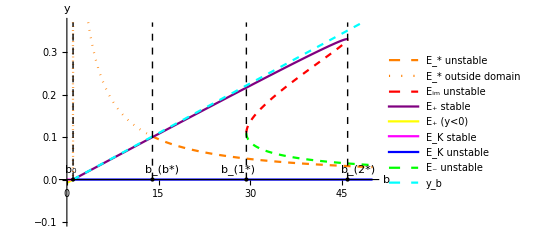

EriB.pdf

```mathematica
cut=cF1;bL=50;max=0.37;
b0n=b0//.cn;
b1=Chop[bbs//.cF1//N];
Print["b0=",b0n//N, " ,b_(b*)=", b1, ", b1*=", bc1, " , b2*=", bc2]
lin1=Line[{{ bc1,0},{ bc1,max}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,max}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
lin3=Line[{{ b0n,0},{ b0n,max}}];
li3=Graphics[{Thick,Black,Dashed,lin3}];
lin4=Line[{{ b1,0},{ b1,max}}];
li4=Graphics[{Thick,Black,Dashed,lin4}];
pyb=Plot[{yb}//.cut,{b,0,bL},PlotStyle->{Dashed,Thick,Cyan},
PlotRange->{{0,200},{0,max}},PlotLegends->{"y_b "}];
(*pym1n=Plot[{ym}//.cut,{b,0,bL},PlotStyle->{Green,Thick},PlotRange->All,PlotPoints->200,
PlotLegends->{"E_- unstable"}];*)

pym=Plot[{ym}//.cut,{b,0,bL},PlotStyle->{Green,Dashed,Thick},PlotRange->All,PlotPoints->180,
PlotLegends->{"E_- unstable"}];
pyK1=Plot[0,{b,0,b0n},PlotStyle->{Magenta},PlotRange->All,PlotLegends->{"E_K stable"}];
pyK2=Plot[0,{b,b0n,bL},PlotStyle->{Blue},PlotRange->All,PlotLegends->{"E_K unstable"}];
pyi=Plot[{yi}//.cut,{b,0, bL},PlotStyle->{Red,Dashed,Thick},PlotRange->All,
PlotLegends->{"E_im unstable"}];
pyp=Plot[{yp}//.cut,{b,b0n,bL},PlotStyle->{Purple, Thick},PlotRange->All,
PlotLegends->{"E_+ stable"}];
pypn=Plot[{yp}//.cut,{b,0,b0n},PlotStyle->{Yellow, Thick},PlotRange->All,
PlotLegends->{"E_+ (y<0)"}];
N[{yp}//.cut/.b->40,20](*check*)
Print["Q(yp) at b0 is "]
Qy/.y->yp/.b->b0//FullSimplify
Show[pyp,pyb,li3,li1,li2,li4];
pys1=Plot[{ys}//.cut,{b,0,b1},PlotStyle->{Orange, Dotted},
PlotRange->{{0,200},{0,max}},
PlotLegends->{"E_* outside domain"}];
pys2=Plot[{ys}//.cut,{b,b1,bL},PlotStyle->{Orange,Thick,Dashed},
PlotRange->{{0,200},{0,max}},
PlotLegends->{"E_* unstable"}];


Print["y*'(b0)=",D[ys,b]/.b->b0n//.cut//N//FullSimplify]
Chop[ys/.b->b0n//.cut//N](*Check*);
bifep1=Show[{pys2,pys1,pyi,pyp,pypn,pyK1,pyK2,pym,pyb,li3,li1,li2,li4},
Epilog->{Text["b_0",Offset[{-2,10},{ b0n//.cut,0}]],{PointSize[Large],
Style[Point[{ b0n//.cut,0}],Black]},
Text["b_(1*)",Offset[{-8,10},{ bc1,0}]],{PointSize[Large],
Style[Point[{ bc1,0}],Purple]},
Text["b_(2*)",Offset[{10,10},{ bc2,0}]],{PointSize[Large],
Style[Point[{ bc2,0}],Yellow]},Text["b_(b*)",Offset[{10,10},{ b1,0}]],{PointSize[Large],
Style[Point[{ b1,0}],Magenta]}},AxesLabel->{"b","y"},PlotRange->{{-0.2,bL},{-0.1,max}}]
Export["EriB.pdf",bifep1]
```

(x,b)-Bifurcation diagram:

Determination of the endemic points with respect to x when ϵ=1:

```mathematica
Solve[((y1)/.vex/.y->yex)==0,z]
```

{{z→(-c γ-(c x λ)/K-β_z √((4 c β_y (x λ-(x^2 λ)/K))/β_z+(-(c γ)/β_z-(c x λ)/(K β_z))^2))/(2 c β_y)},{z→(-c γ-(c x λ)/K+β_z √((4 c β_y (x λ-(x^2 λ)/K))/β_z+(-(c γ)/β_z-(c x λ)/(K β_z))^2))/(2 c β_y)}}

```mathematica
yex=c z/βz;(*Frome Solve[(z1/z/.cep1)==0,y]*)
Print["ye(x)=",yex]
Print["ve(x)="]
vex=Solve[(x1/x)==0,v][[1]]
Print["ze(x)="]
zex=Solve[((y1/y)/.vex/.y->yex)==0,z][[1]]//FullSimplify
(*the first solution of z above doesn't belong to the domain*)
vnn=(v1/v/.vex/.y->yex/.zex );
vnnn=vnn/.cF1
xex=Solve[vnnn==0,x,Cubics->False];
(*or // ComplexExpand[#, TargetFunctions -> {Re, Im}] &*)
(*so long time when it's not numeric**)

Print["Number of endemic x"]
Length[xex]
Print["Numerical check"]
xex/.b->40//N
```

ye(x)=(c z)/β_z

ve(x)=

{v→((K-x-y) λ)/(K β)}

ze(x)=

{z→(-c (K γ+x λ)+√(c (4 K (K-x) x β_y β_z λ+c (K γ+x λ)^2)))/(2 c K β_y)}

(87 (1/256 b (-1/128-x+√(4 (1-x) x+(1/128+x)^2))-x (1-x+1/2 (1/128+x-√(4 (1-x) x+(1/128+x)^2)))-1/87 (-1/128-x+√(4 (1-x) x+(1/128+x)^2)) (1-x+1/2 (1/128+x-√(4 (1-x) x+(1/128+x)^2)))+1/87 (-1+x+1/2 (-1/128-x+√(4 (1-x) x+(1/128+x)^2)))))/(2 (1-x+1/2 (1/128+x-√(4 (1-x) x+(1/128+x)^2))))

Solve::nongen: Solutions may not be valid for all values of parameters.

Number of endemic x

3

Numerical check

{{x→0.00262408},{x→0.114678},{x→0.540959}}

```mathematica
(*Jacobians of the fixed points**)
jEsx=jacD/.cep1/.sol[[3]]/.z->0;
jEmx=jacD/.cep1/.vex/.y->yex/.zex/.xex[[1]];
jEimx=jacD/.cep1/.vex/.y->yex/.zex/.xex[[2]];
jEpx=jacD/.cep1/.vex/.y->yex/.zex/.xex[[3]];
(*Checks on the stability of the fixed points**)
Print["Eigenvalues of E* : "]
Print[" between b0 and b1* "]
Eigenvalues[jEsx]//.cF1/.b->15//N
Print[" between b1* and b2* "]
Eigenvalues[jEsx]//.cF1/.b->40//N
Print["Eigenvalues of E+  between b1* and b2*"]
Chop[Eigenvalues[jEpx//.cF1/.b->42//N]]
Print["Eigenvalues of Eim  between b1* and b2*"]
Chop[Eigenvalues[jEimx//.cF1/.b->35//N]]
Print["Eigenvalues of E- between b0 and b1* "]
Chop[Eigenvalues[jEmx//.cF1/.b->15//N]]
Print["Eigenvalues of E-  between b1* and b2*"]
Chop[Eigenvalues[jEimx//.cF1/.b->40//N]]
Print["Eigenvalues of E-  after b2*"]
Chop[Eigenvalues[jEimx//.cF1/.b->50//N]]
```

Eigenvalues of E* :

between b0 and b1*

{0.0950185,-0.606269,0.0309604-0.074022 ⅈ,0.0309604+0.074022 ⅈ}

between b1* and b2*

{0.0363426,-0.555066,0.017069-0.082122 ⅈ,0.017069+0.082122 ⅈ}

Eigenvalues of E+  between b1* and b2*

{-22.81,-0.157506+0.275785 ⅈ,-0.157506-0.275785 ⅈ,-0.301641}

Eigenvalues of Eim  between b1* and b2*

{-4.10357,0.346228,-0.0664887+0.180685 ⅈ,-0.0664887-0.180685 ⅈ}

Eigenvalues of E- between b0 and b1*

{-38.9444,-0.864225,-0.053898+0.0931984 ⅈ,-0.053898-0.0931984 ⅈ}

Eigenvalues of E-  between b1* and b2*

{-6.50192,0.307571,-0.103153+0.233849 ⅈ,-0.103153-0.233849 ⅈ}

Eigenvalues of E-  after b2*

{-14.0734+7.77106 ⅈ,-0.136004+0.346012 ⅈ,-0.181515-0.313963 ⅈ,-0.00338735+0.318699 ⅈ}

128.989

bH=1.152364263 ,b1*=29.361 ,b2*=45.9232

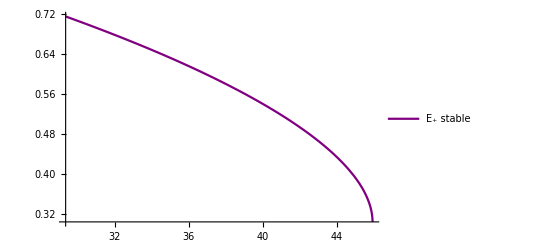

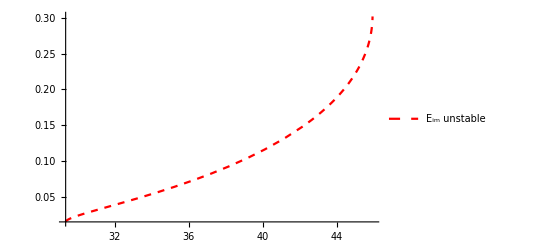

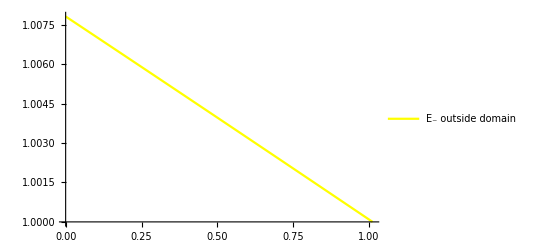

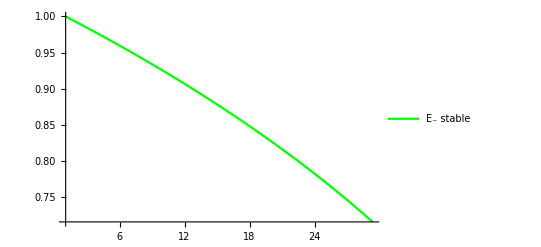

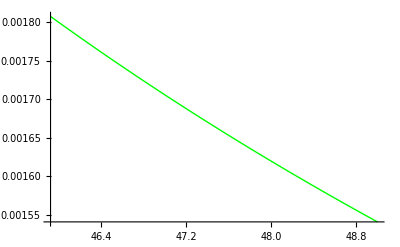

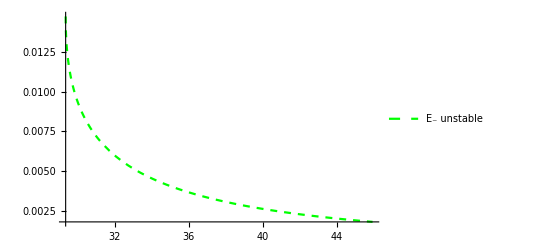

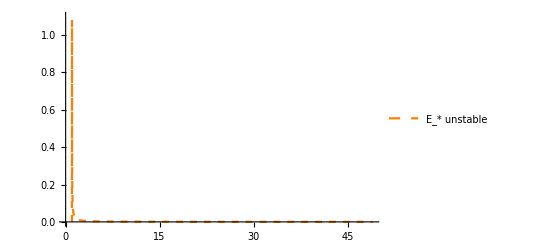

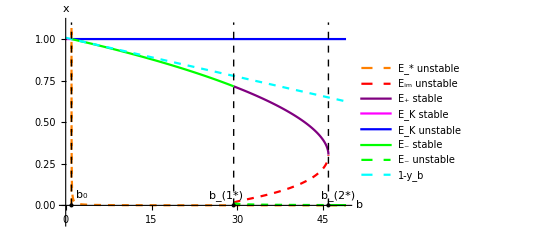

Bif1x.pdf

```mathematica
cut=cF1;bL=49;max=1.1;
b0n=b0//.cn;
b1=Chop[b/.Solve[(Es1[[1]])==(1-yb),b][[2]]//.cF1//N]
Print["bH=",bH, " ,b1*=",bc1, " ,b2*=",bc2]
lin1=Line[{{ bc1,0},{ bc1,max}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,max}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
lin3=Line[{{ b0n,0},{ b0n,max}}];
li3=Graphics[{Thick,Black,Dashed,lin3}];
lin4=Line[{{ b1,0},{ b1,max}}];
li4=Graphics[{Thick,Black,Dashed,lin4}];
pxp=Plot[{x/.xex[[3]]}//.cut,{b,0,bL},PlotStyle->{Purple,Thick},PlotRange->All,PlotPoints->180,
PlotLegends->{"E_+ stable"}]
pxK1=Plot[K//.cut,{b,0,b0n},PlotStyle->{Magenta},PlotRange->All,PlotLegends->{"E_K stable"}];
pxK2=Plot[K//.cut,{b,b0n,bL},PlotStyle->{Blue},PlotRange->All,PlotLegends->{"E_K unstable"}];
pxi=Plot[{x/.xex[[2]]}//.cut,{b,b0n, bL},PlotStyle->{Red, Dashed,Thick},PlotRange->All,
PlotLegends->{"E_im unstable"}]
pxm0=Plot[{x/.xex[[1]]}//.cut,{b,0,b0n},PlotStyle->{Yellow,  Thick},PlotRange->All,
PlotLegends->{"E_- outside domain "}]
pxm=Plot[{x/.xex[[1]]}//.cut,{b,b0n,bc1},PlotStyle->{Green,  Thick},PlotRange->All,
PlotLegends->{"E_- stable"}]
pxm1=Plot[{x/.xex[[1]]}//.cut,{b,bc2,bL},PlotStyle->{Green, Thick},PlotRange->All,PlotPoints->40]
pxm2=Plot[{x/.xex[[1]]}//.cut,{b,bc1,bc2},PlotStyle->{Green,Dashed,  Thick},PlotRange->All,
PlotLegends->{"E_- unstable"}]

pxs=Plot[{x/.sol[[3]]}//.cut,{b,0,bL},PlotStyle->{Orange,Thick,Dashed},
PlotRange->{{0,bL},{0,max}},
PlotLegends->{"E_* unstable"}]

pxb=Plot[{1-yb}//.cut,{b,0,bL},PlotStyle->{Dashed,Thick,Cyan},
PlotRange->{{0,bL},{0,max}},PlotLegends->{"1-y_b "}];

bifep1=Show[{pxs,pxi,pxp,pxK1,pxK2,pxm,pxm1,pxm2,(*pxm0,*)pxb,li3,li1,li2,li4},
Epilog->{Text["b_0",Offset[{10,10},{ b0n//.cut,0}]],{PointSize[Large],
Style[Point[{ b0n//.cut,0}],Black]},
Text["b_(1*)",Offset[{-8,10},{ bc1,0}]],{PointSize[Large],
Style[Point[{ bc1,0}],Purple]},
Text["b_(2*)",Offset[{10,10},{ bc2,0}]],{PointSize[Large],
Style[Point[{ bc2,0}],Yellow]},Text["b_(b*)",Offset[{0,10},{ b1,0}]],{PointSize[Large],
Style[Point[{ b1,0}],Magenta]}},AxesLabel->{"b","x"},PlotRange->{{-0.1,bL},{-0.1,max}}]
Export["Bif1x.pdf",bifep1]
```

```mathematica
(*Some checks*)
Print["between b0 and b1*; E-="]
{x/.xex[[2]],yex[[2]]/.zex/.xex[[2]],v/.vex/.y->yex/.(zex)/.xex[[2]],z/.zex/.xex[[2]]}//.cut/.b->15//N
Print["with yb="]
yb//.cut/.b->15//N
Print["between b1* and b2*; E-="]
{x/.xex[[2]],yex[[2]]/.zex/.xex[[2]],v/.vex/.y->yex/.(zex)/.xex[[2]],z/.zex/.xex[[2]]}//.cut/.b->35//N
Print[" after b2*; E-="]
{x/.xex[[2]],yex[[2]]/.zex/.xex[[2]],v/.vex/.y->yex/.(zex)/.xex[[2]],z/.zex/.xex[[2]]}//.cut/.b->47//N
Print["between  b0 and  b1*; E*="]
sol[[3]]//.cut/.b->15//N
Print[" between b1* and  b2*; E*="]
sol[[3]]//.cut/.b->35//N
Print["After  b2*; E*="]
sol[[3]]//.cut/.b->47//N
```

between b0 and b1*; E-=

{0.878336,0.107541,0.000324678,0.107541}

with yb=

0.109375

between b1* and b2*; E-=

{0.00405931,0.0579238,0.0215636,0.0579238}

after b2*; E-=

{0.0017057,0.0367794,0.0221038,0.0367794}

between  b0 and  b1*; E*=

{x→0.000821018,y→0.0950185,v→0.0207853}

between b1* and  b2*; E*=

{x→0.000338066,y→0.0414636,v→0.0220275}

After  b2*; E*=

{x→0.000249875,y→0.030985,v→0.0222705}

```mathematica
(*Endemic x using the elimination**)
elx=Eliminate[Thread[({x1/x,y1/y,v1,z1/z}/.cep1/.cKga1)=={0,0,0,0}],{y,v,z}];
Qx=(elx[[1]]-elx[[2]]);
Print["Coefficients of  Qx by elim polynomial are:"]
cofx=CoefficientList[Qx,x]//FullSimplify;
Length[cofx]
solx=x/.Solve[Qx==0,x,Cubics->False](*Third order roots*)
solx//.cF1/.b->40//N
```

Coefficients of  Qx by elim polynomial are:

4

{Root[-b c^2 β β_y δ+c^2 β_v δ λ+c β_v β_y β_z δ λ-c^2 β_y δ^2 λ-c β_y^2 β_z δ^2 λ+(-b c^2 β^2 β_y+b^2 c^2 β^2 β_y+c^2 β β_v λ-b c^2 β β_v λ+c β β_v β_y β_z λ-2 b c β β_v β_y β_z λ-2 c^2 β β_y δ λ+b c^2 β β_y δ λ-c β_v β_y β_z δ λ-2 c β β_y^2 β_z δ λ+c β_y^2 β_z δ^2 λ+c β_v^2 β_z λ^2+β_v^2 β_y β_z^2 λ^2+c^2 β_v δ λ^2+c β_v β_y β_z δ λ^2) #1+(-c^2 β^2 β_y λ+b c^2 β^2 β_y λ-c β β_v β_y β_z λ+2 b c β β_v β_y β_z λ-c β^2 β_y^2 β_z λ+2 c β β_y^2 β_z δ λ+c^2 β β_v λ^2-b c^2 β β_v λ^2-c β_v^2 β_z λ^2+c β β_v β_y β_z λ^2-2 β_v^2 β_y β_z^2 λ^2-c β_v β_y β_z δ λ^2) #1^2+(c β^2 β_y^2 β_z λ-c β β_v β_y β_z λ^2+β_v^2 β_y β_z^2 λ^2) #1^3&,1],Root[-b c^2 β β_y δ+c^2 β_v δ λ+c β_v β_y β_z δ λ-c^2 β_y δ^2 λ-c β_y^2 β_z δ^2 λ+(-b c^2 β^2 β_y+b^2 c^2 β^2 β_y+c^2 β β_v λ-b c^2 β β_v λ+c β β_v β_y β_z λ-2 b c β β_v β_y β_z λ-2 c^2 β β_y δ λ+b c^2 β β_y δ λ-c β_v β_y β_z δ λ-2 c β β_y^2 β_z δ λ+c β_y^2 β_z δ^2 λ+c β_v^2 β_z λ^2+β_v^2 β_y β_z^2 λ^2+c^2 β_v δ λ^2+c β_v β_y β_z δ λ^2) #1+(-c^2 β^2 β_y λ+b c^2 β^2 β_y λ-c β β_v β_y β_z λ+2 b c β β_v β_y β_z λ-c β^2 β_y^2 β_z λ+2 c β β_y^2 β_z δ λ+c^2 β β_v λ^2-b c^2 β β_v λ^2-c β_v^2 β_z λ^2+c β β_v β_y β_z λ^2-2 β_v^2 β_y β_z^2 λ^2-c β_v β_y β_z δ λ^2) #1^2+(c β^2 β_y^2 β_z λ-c β β_v β_y β_z λ^2+β_v^2 β_y β_z^2 λ^2) #1^3&,2],Root[-b c^2 β β_y δ+c^2 β_v δ λ+c β_v β_y β_z δ λ-c^2 β_y δ^2 λ-c β_y^2 β_z δ^2 λ+(-b c^2 β^2 β_y+b^2 c^2 β^2 β_y+c^2 β β_v λ-b c^2 β β_v λ+c β β_v β_y β_z λ-2 b c β β_v β_y β_z λ-2 c^2 β β_y δ λ+b c^2 β β_y δ λ-c β_v β_y β_z δ λ-2 c β β_y^2 β_z δ λ+c β_y^2 β_z δ^2 λ+c β_v^2 β_z λ^2+β_v^2 β_y β_z^2 λ^2+c^2 β_v δ λ^2+c β_v β_y β_z δ λ^2) #1+(-c^2 β^2 β_y λ+b c^2 β^2 β_y λ-c β β_v β_y β_z λ+2 b c β β_v β_y β_z λ-c β^2 β_y^2 β_z λ+2 c β β_y^2 β_z δ λ+c^2 β β_v λ^2-b c^2 β β_v λ^2-c β_v^2 β_z λ^2+c β β_v β_y β_z λ^2-2 β_v^2 β_y β_z^2 λ^2-c β_v β_y β_z δ λ^2) #1^2+(c β^2 β_y^2 β_z λ-c β β_v β_y β_z λ^2+β_v^2 β_y β_z^2 λ^2) #1^3&,3]}

{0.000294987,-19.9296-34.5878 ⅈ,-19.9296+34.5878 ⅈ}